# NG^23 T_03. Метод главных компонент

КМ2021, курс 2, семестр 4
Ковалевская Варвара
20-фев-2023

## Задание 1

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Data = Import["NG23T03Problem.xlsx",{"Data",1}]]
```

{763,25}

```mathematica
Attr = Data[[4,2;;]]
```

{Возраст,Рост,Высота глаз стоя,Высота плеча стоя,Высота локтя стоя,Высота кулака стоя,Вертикальная хватка,Высота макушки сидя,Высота глаз сидя,Высота плеча сидя,Высота локтя сидя,Высота подколенного сустава,Толщина бедра,Ягодично-подколенная длина,Длина от ягодиц до колена,Длина руки до локтя,Длина руки,Глубина живота,Ширина бёдер,Ширина плеч,Длина ладони,Ширина ладони,Длина ступни,Ширина ступни}

```mathematica
ClearAll[Train,Test];
Map[Dimensions,{Train,Test} = TakeDrop[RandomSample@#,Round[0.8 Length @#]]&@Data[[5;;]]]
Map[Dimensions,{TrainLabel, Train}={Train[[All,1]],Train[[All,2;;]]}]
Map[Dimensions,{TestLabel, Test}={Test[[All,1]],Test[[All,2;;]]}]
```

{{607,25},{152,25}}

{{607},{607,24}}

{{152},{152,24}}

```mathematica
Length[indMale = Flatten@Position[TrainLabel,"М"]]
Length[indFemale = Flatten@Position[TrainLabel,"Ж"]]
```

297

310

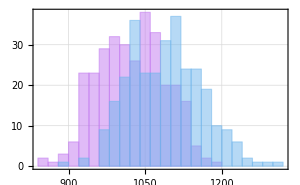

```mathematica
Histogram[{Train[[indFemale,5]],Train[[indMale,5]]},Frame->True,ImageSize->300,GridLines->Automatic,ChartStyle->"Pastel"]
```

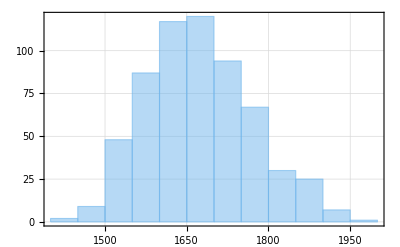
Рост
-Graphics-

```mathematica
TableForm[{Text[Attr⟦2⟧],Histogram[{Train[[All,2]]},Frame->True,GridLines->Automatic,ChartStyle->"Pastel"]},TableAlignments->Center]
```

```mathematica
Manipulate[{TableForm[{Text[Attr⟦n⟧],Histogram[{Train[[All,n]]},Frame->True,GridLines->Automatic,ChartStyle->"Pastel"]},TableAlignments->Center]},Row[{Control[{{n,21},1,23,1,SetterBar}]}]]
```

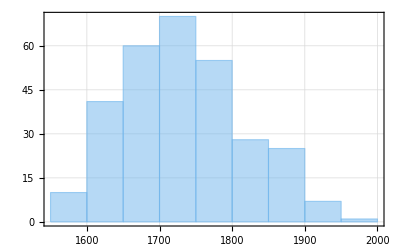
Рост
-Graphics-

```mathematica
TableForm[{Text[Attr⟦2⟧],Histogram[{Train[[indMale,2]]},Frame->True,GridLines->Automatic,ChartStyle->"Pastel"]},TableAlignments->Center]
```

```mathematica
Manipulate[{TableForm[{Text[Attr⟦n⟧],Histogram[{Train[[indMale,n]],Train[[indFemale,n]]},Frame->True,GridLines->Automatic,ChartStyle->"Pastel"]},TableAlignments->Center]},Row[{Control[{{n,21},1,23,1,SetterBar}]}]]
```

```mathematica
Manipulate[{TableForm[{Text[Attr⟦n⟧],Histogram[{Train[[All,n]]},Frame->True,GridLines->Automatic,ChartStyle->"Pastel"]},TableAlignments->Center],TableForm[{Text[Attr⟦n⟧],Histogram[{Train[[indMale,n]],Train[[indFemale,n]]},Frame->True,GridLines->Automatic,ChartStyle->"Pastel"]},TableAlignments->Center]}⟦part⟧,Row[{Control[{{n,21},1,23,1,SetterBar}]}],{part, {1-> "All",2->"M/F"}},ImageMargins->Medium]
```

## Задание 2

```mathematica
Dimensions[Stat = Through@{Mean,StandardDeviation}@Train]
```

{2,24}

```mathematica
Stat[[All,11]]
Through@{Mean,StandardDeviation}@Train[[All,11]]
Through@{Mean,StandardDeviation}@Train[[All,7]]
```

{233.557,25.3444}

{233.557,25.3444}

{1890.97,172.439}

```mathematica
ClearAll[stdTrain];
Dimensions[stdTrain=MapThread[(#1-First@#2)/(Last@#2)&,{Trainᵀ,Statᵀ}]ᵀ]
```

{607,24}

```mathematica
Map[Dimensions,{Train,Trainᵀ,Stat}]
```

{{607,24},{24,607},{2,24}}

## Задание 3

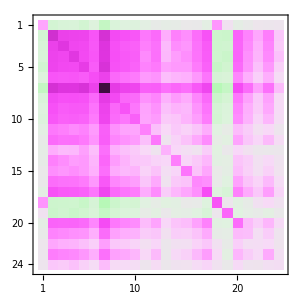

```mathematica
MatrixPlot[Cov = Covariance@Train,ImageSize->300,ColorFunction->"GreenPinkTones"]
```

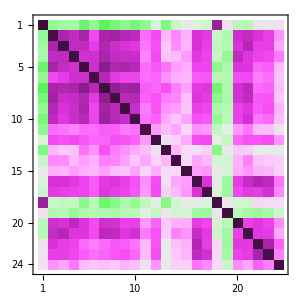
{-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[Cov = Covariance@Train,ImageSize->300,ColorFunction->"GreenPinkTones"],MatrixPlot[stdCov = Covariance@stdTrain,ImageSize->300,ColorFunction->"GreenPinkTones"]}
```

```mathematica
ClearAll[kmMatrixPlot];
kmMatrixPlot[M_,opts___]:=MatrixPlot[Rescale[M,{-#,#}&@Max@Abs@M],ColorFunctionScaling->False,LabelStyle->Black,ColorFunction->(If[0.49<#<0.51,White,ColorData["GreenPinkTones",#]]&),
opts]
```

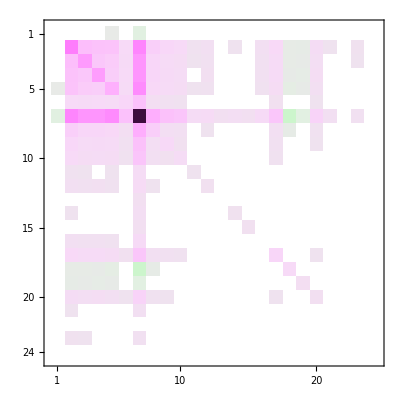

```mathematica
kmMatrixPlot[Cov]
```

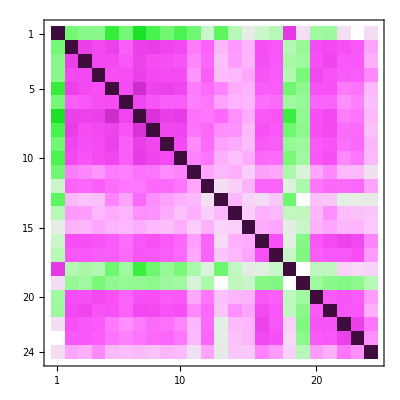

```mathematica
kmMatrixPlot[stdCov]
```

## Задание 4

```mathematica
∫_(μ+σ)^(μ+2 σ) 1/(σ √(2 π)) ⅇ^((- (x-μ)^2)/(2 σ^2))ⅆx//N
```

0.135905

```mathematica
Flatten@{-∞,μ+Range[-3,3] σ,∞}
Partition[%,2,1]
Integrate[1./(σ √(2. π)) ⅇ^((- (x-μ)^2)/(2. σ^2)),{x,##}]&@@@%
```

{-∞,μ-3 σ,μ-2 σ,μ-σ,μ,μ+σ,μ+2 σ,μ+3 σ,∞}

{{-∞,μ-3 σ},{μ-3 σ,μ-2 σ},{μ-2 σ,μ-σ},{μ-σ,μ},{μ,μ+σ},{μ+σ,μ+2 σ},{μ+2 σ,μ+3 σ},{μ+3 σ,∞}}

{ConditionalExpression[1/σ 0.398942 (1.25331/(√(1/σ^2))-(1.25331 Erf[0.707107 μ √(1/σ^2)])/(√(1/σ^2))+(1.25331 μ Erf[0.707107 √(μ^2/σ^2)])/(√(μ^2/σ^2))-(1.25331 (-5.23364×10^-17 μ+1. σ) Erf[2.12132 √(((5.23364×10^-17 μ-1. σ)^2)/σ^2)])/(√(((5.23364×10^-17 μ-1. σ)^2)/σ^2))), (Re[μ/σ^2]<0||Re[σ^2]>0)&&Re[σ^2]≥0],0.0214002,0.135905,0.341345,0.341345,0.135905,0.0214002,ConditionalExpression[1/σ 0.398942 (1.25331/(√(1/σ^2))+(1.25331 Erf[0.707107 μ √(1/σ^2)])/(√(1/σ^2))-(1.25331 μ Erf[0.707107 √(μ^2/σ^2)])/(√(μ^2/σ^2))-(1.25331 (5.23364×10^-17 μ+1. σ) Erf[2.12132 √(((5.23364×10^-17 μ+1. σ)^2)/σ^2)])/(√(((5.23364×10^-17 μ+1. σ)^2)/σ^2))), (Re[μ/σ^2]<0||Re[σ^2]>0)&&Re[σ^2]≥0]}

```mathematica
Flatten@{-∞,μ+Range[-3,3] σ,∞}
Partition[%,2,1]
N@Integrate[1./(σ √(2. π)) ⅇ^((- (x-μ)^2)/(2. σ^2)),{x,##}]&@@@%
```

{-∞,μ-3 σ,μ-2 σ,μ-σ,μ,μ+σ,μ+2 σ,μ+3 σ,∞}

{{-∞,μ-3 σ},{μ-3 σ,μ-2 σ},{μ-2 σ,μ-σ},{μ-σ,μ},{μ,μ+σ},{μ+σ,μ+2 σ},{μ+2 σ,μ+3 σ},{μ+3 σ,∞}}

{ConditionalExpression[1/σ 0.398942 (1.25331/(√(1/σ^2))-(1.25331 Erf[0.707107 μ √(1/σ^2)])/(√(1/σ^2))+(1.25331 μ Erf[0.707107 √(μ^2/σ^2)])/(√(μ^2/σ^2))-(1.25331 (-5.23364×10^-17 μ+1. σ) Erf[2.12132 √(((5.23364×10^-17 μ-1. σ)^2)/σ^2)])/(√(((5.23364×10^-17 μ-1. σ)^2)/σ^2))), (Re[μ/σ^2]<0.||Re[σ^2]>0.)&&Re[σ^2]≥0.],0.0214002,0.135905,0.341345,0.341345,0.135905,0.0214002,ConditionalExpression[1/σ 0.398942 (1.25331/(√(1/σ^2))+(1.25331 Erf[0.707107 μ √(1/σ^2)])/(√(1/σ^2))-(1.25331 μ Erf[0.707107 √(μ^2/σ^2)])/(√(μ^2/σ^2))-(1.25331 (5.23364×10^-17 μ+1. σ) Erf[2.12132 √(((5.23364×10^-17 μ+1. σ)^2)/σ^2)])/(√(((5.23364×10^-17 μ+1. σ)^2)/σ^2))), (Re[μ/σ^2]<0.||Re[σ^2]>0.)&&Re[σ^2]≥0.]}

```mathematica
Stat[[All,19]]
Flatten@{-∞,First@Stat[[All,19]]+Range[-3,3] Last@Stat[[All,19]],∞}
N@BinCounts[Train[[All,19]],{%}]/Length@Train
PercentForm[#,{∞,2}]&/@%
```

{389.516,34.3644}

{-∞,286.422,320.787,355.151,389.516,423.88,458.244,492.609,∞}

{0.00164745,0.0181219,0.146623,0.339374,0.341021,0.130148,0.0214168,0.00164745}

{0.16%,1.81%,14.66%,33.94%,34.10%,13.01%,2.14%,0.16%}

```mathematica
Stat[[All,19]]
Flatten@{-∞,First@Stat[[All,19]]+Range[-3,3] Last@Stat[[All,19]],∞}
N[BinCounts[Train[[All,19]],{Flatten@{-∞,First@Stat[[All,19]]+Range[-3,3] Last@Stat[[All,19]],∞}}]/Length@Train]
PercentForm[#,{∞,2}]&/@N[BinCounts[Train[[All,19]],{Flatten@{-∞,First@Stat[[All,19]]+Range[-3,3] Last@Stat[[All,19]],∞}}]/Length@Train]
```

{389.516,34.3644}

{-∞,286.422,320.787,355.151,389.516,423.88,458.244,492.609,∞}

{0.00164745,0.0181219,0.146623,0.339374,0.341021,0.130148,0.0214168,0.00164745}

{0.16%,1.81%,14.66%,33.94%,34.10%,13.01%,2.14%,0.16%}

```mathematica
Grid[Table[PercentForm[#,{∞,2}]&/@N[BinCounts[Train[[All,m]],{Flatten@{-∞,First@Stat[[All,m]]+Range[-3,3] Last@Stat[[All,m]],∞}}]/Length@Train],{m,1,24}]]
```

0.00% | 0.00% | 20.76% | 24.38% | 36.90% | 17.96% | 0.00% | 0.00%
0.00% | 0.82% | 15.98% | 36.57% | 30.15% | 12.36% | 3.79% | 0.33%
0.00% | 1.81% | 13.67% | 35.75% | 31.96% | 14.50% | 2.31% | 0.00%
0.00% | 1.81% | 15.16% | 34.43% | 31.14% | 15.16% | 2.31% | 0.00%
0.00% | 0.82% | 16.31% | 34.27% | 32.95% | 13.01% | 2.31% | 0.33%
0.16% | 1.65% | 15.82% | 30.97% | 34.76% | 14.83% | 1.65% | 0.16%
0.00% | 0.99% | 16.47% | 34.10% | 30.97% | 15.16% | 2.31% | 0.00%
0.16% | 2.47% | 14.17% | 32.95% | 33.77% | 15.32% | 1.15% | 0.00%
0.00% | 0.82% | 16.47% | 33.11% | 34.27% | 12.19% | 3.13% | 0.00%
0.00% | 0.99% | 15.98% | 34.10% | 31.30% | 15.65% | 1.98% | 0.00%
0.00% | 1.98% | 14.17% | 34.60% | 32.45% | 14.33% | 2.31% | 0.16%
0.16% | 2.80% | 12.19% | 35.75% | 33.28% | 13.34% | 2.31% | 0.16%
0.00% | 2.47% | 15.16% | 31.80% | 34.93% | 13.18% | 2.14% | 0.33%
0.16% | 1.65% | 15.16% | 33.77% | 32.45% | 15.32% | 1.48% | 0.00%
0.00% | 2.47% | 12.19% | 38.71% | 30.64% | 13.34% | 2.47% | 0.16%
0.00% | 1.48% | 13.67% | 37.07% | 31.80% | 13.01% | 2.97% | 0.00%
0.00% | 1.15% | 14.50% | 35.91% | 30.97% | 14.33% | 2.97% | 0.16%
0.00% | 1.81% | 13.51% | 37.73% | 29.32% | 15.16% | 2.47% | 0.00%
0.16% | 1.48% | 14.50% | 34.27% | 33.77% | 13.34% | 2.47% | 0.00%
0.00% | 1.65% | 14.00% | 37.40% | 30.64% | 13.34% | 2.80% | 0.16%
0.00% | 1.65% | 15.65% | 34.93% | 30.64% | 14.99% | 2.14% | 0.00%
0.00% | 0.16% | 20.43% | 29.65% | 30.31% | 17.63% | 1.81% | 0.00%
0.00% | 1.65% | 15.32% | 33.94% | 30.64% | 16.80% | 1.48% | 0.16%
0.00% | 1.65% | 16.31% | 33.11% | 32.95% | 13.01% | 2.64% | 0.33%

```mathematica
Dynamic@Grid[{Flatten@{-∞,μ+Range[-3,3] σ,∞},(PercentForm[#,{∞,2}]&/@N[BinCounts[Train[[All,##]],{Flatten@{-∞,First@Stat[[All,##]]+Range[-3,3] Last@Stat[[All,##]],∞}}]/Length@Train])&/@Range[1,24]},Frame->All,Background->{None,{LightGray,LightBlue}}];
```

```mathematica
DynamicModule[{m=2},Column[{Row@{"Параметр: ",SetterBar[Dynamic@m,Range[1,24]]},Dynamic@Grid[{Flatten@{-∞,μ+Range[-3,3] σ,∞},(PercentForm[#,{∞,2}]&/@N[BinCounts[Train[[All,m]],{Flatten@{-∞,First@Stat[[All,m]]+Range[-3,3] Last@Stat[[All,m]],∞}}]/Length@Train])},Frame->All,Background->{None,{LightGray,LightBlue}}]},Center,Frame->All,Background->{LightMagenta,LightMagenta}]]
```

## Задание 5

```mathematica
{11,19};
Through@{Mean,Covariance}@Train[[All,%]]
```

{{233.557,389.516},{{642.336,-75.385},{-75.385,1180.91}}}

{{233.557,389.516},{{642.336,-75.385},{-75.385,1180.91}}}

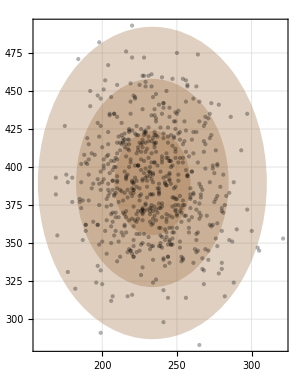

```mathematica
{11,19};
Through@{Mean,Covariance}@Train[[All,%]]
Graphics[{Opacity[.3,Brown],Ellipsoid@@%,Apply[Ellipsoid[#1,4 #2]&,%],Apply[Ellipsoid[#1,9 #2]&,%],
PointSize@Small,Black,Point@Train[[All,%%]]},Frame->True,ImageSize->{300,Automatic},GridLines->Automatic]
```

{{7.66822×10^-16,-1.01539×10^-15},{{1.,0.296937},{0.296937,1.}}}

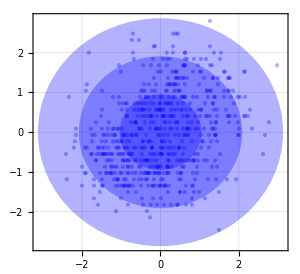

```mathematica
{10,22};
Through@{Mean,Covariance}@stdTrain[[All,%]]
Graphics[{Opacity[.3,Blue],Ellipsoid@@%,Apply[Ellipsoid[#1,4 #2]&,%],Apply[Ellipsoid[#1,9 #2]&,%],
PointSize@Small,Blue,Point@stdTrain[[All,%%]]},Frame->True,ImageSize->300,GridLines->Automatic]
(*точек, лежащих за пределами 3σ практически нет*)
```

```mathematica
{11,19};
Through@{Mean,Covariance}@Train[[All,{11,19}]]
Graphics[{Opacity[.3,Brown],Ellipsoid@@Through@{Mean,Covariance}@Train[[All,{11,19}]],Apply[Ellipsoid[#1,4 #2]&,Through@{Mean,Covariance}@Train[[All,{11,19}]]],Apply[Ellipsoid[#1,9 #2]&,Through@{Mean,Covariance}@Train[[All,{11,19}]]],
PointSize@Small,Black,Point@Train[[All,{11,19}]]},Frame->True,ImageSize->{300,Automatic},GridLines->Automatic]
```

{{233.557,389.516},{{642.336,-75.385},{-75.385,1180.91}}}

-Graphics-

## Задание 6

{{607,607},{607,24},{24,24}}

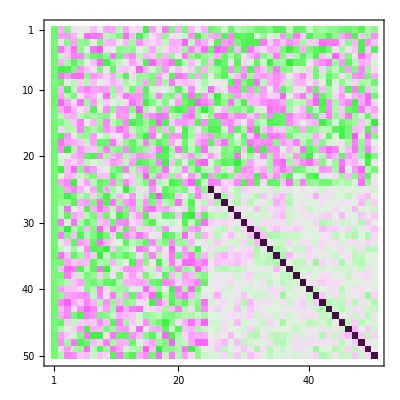
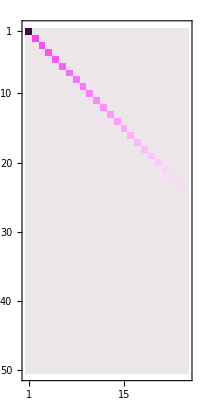
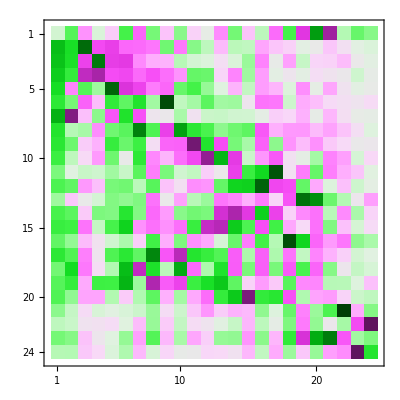

```mathematica
Map[Dimensions,{U,S,V}=SingularValueDecomposition@Train]
MatrixPlot[#,ImageSize->{Automatic,150},ColorFunction->"GreenPinkTones"]&/@{Take[U,50,50],Take[S,50],V}
```

```mathematica
MinMax[Train-U.S.Vᵀ]
```

{-1.60298×10^-11,3.70619×10^-11}

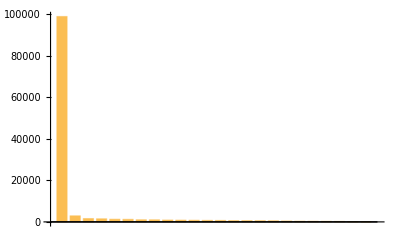

```mathematica
BarChart[Diagonal@S]
```

## Задание 7

```mathematica
Dimensions[pcTrain = stdTrain.V]
```

{607,24}

```mathematica
stdTrain[[123]].V
```

{-3.09271,-0.181391,0.833273,0.035844,-0.322064,1.35226,-0.882081,-1.19774,0.853889,1.02439,0.338283,2.32527,-0.125429,1.44569,0.823179,-0.481158,0.727679,-0.440345,-0.497935,1.11547,-0.434256,-1.16753,1.81526,1.27886}

```mathematica
Dimensions[ StatPC= Through@{Mean,StandardDeviation}@pcTrain]
```

{2,24}

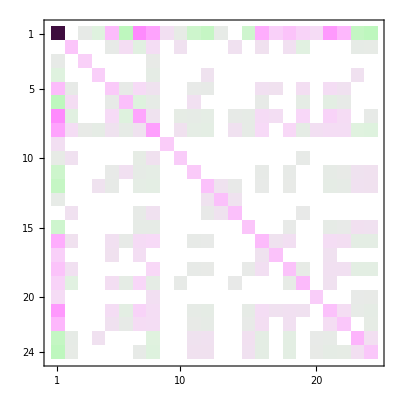

```mathematica
kmMatrixPlot[CovPC]
```

## Задание 8

```mathematica
Dimensions[Cov]
```

{24,24}

```mathematica
Dimensions[ muMale= Mean@Train[[indMale]]]
Dimensions[ muFemale= Mean@Train[[indFemale]]]
```

{24}

{24}

```mathematica
Dimensions@Thread[muMale-muFemale]
```

{24}

```mathematica
W=Inverse[Cov].(Thread[muMale-muFemale])
```

{0.0179535,0.00223558,0.00192853,0.0023892,0.000293996,0.00132126,-0.000406567,0.00241378,0.00401442,0.00309564,0.00159713,0.00895599,-0.0129794,-0.00155021,0.00125776,0.00775966,0.00276704,0.0057052,-0.00201142,0.00534025,0.00874708,0.0674309,0.0169119,0.0300812}

```mathematica
W0=1/2 (muMale.Inverse[Cov].muMale-muFemale.Inverse[Cov].muFemale)
```

42.9052